```mathematica
k={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

```mathematica
k[[40]]
```

0

```mathematica
a={0.0445847082,0.0053219268,-0.0084664166,-0.0083147273,-0.0040144738,-0.0009224968,0.0002427978,0.0003657739,0.0001995134,0.0000604410,0.0000005905,-0.0000115632,-0.0000078079,-0.0000029393,-0.0000004480,0.0000002609,0.0000002542,0.0000001170,0.0000000291,-0.0000000025,0.0445847082,0.0053219268,-0.0084664166,-0.0083147273,-0.0040144738,-0.0009224968,0.0002427978,0.0003657739,0.0001995134,0.0000604410,0.0000005905,-0.0000115632,-0.0000078079,-0.0000029393,-0.0000004480,0.0000002609,0.0000002542,0.0000001170,0.0000000291,-0.0000000025};
b={0.0078380943,0.0196787186,0.0099532406,0.0014340540,0.0018089515,0.0017977759,0.0008953215,0.0002348651,0.0000283129,0.0000682241,0.0000405632,0.0000137208,0.0000012286,0.0000018294,0.0000014393,0.0000005988,0.0000001218,0.0000000320,0.0000000433,0.0000000220,0.0078380943,0.0196787186,0.0099532406,0.0014340540,0.0018089515,0.0017977759,0.0008953215,0.0002348651,0.0000283129,0.0000682241,0.0000405632,0.0000137208,0.0000012286,0.0000018294,0.0000014393,0.0000005988,0.0000001218,0.0000000320,0.0000000433,0.0000000220};
```

```mathematica
For [i=1,i≤20,i++,
k[[i]]=i*Pi/40;];
(*f[x_]:=a[[i]]*Cos[k[[i]]*x]=b[[i]]*Sin[k[[i]]*x]*)

For [i=21,i≤40,i++,
k[[i]]=(i-20)*Pi/40;];
```

```mathematica
coskx[x_]:={Cos[k[[1]]*x],Cos[k[[2]]*x],Cos[k[[3]]*x],Cos[k[[4]]*x],Cos[k[[5]]*x],Cos[k[[6]]*x],Cos[k[[7]]*x],Cos[k[[8]]*x],Cos[k[[9]]*x],Cos[k[[10]]*x],Cos[k[[11]]*x],Cos[k[[12]]*x],Cos[k[[13]]*x],Cos[k[[14]]*x],Cos[k[[15]]*x],Cos[k[[16]]*x],Cos[k[[17]]*x],Cos[k[[18]]*x],Cos[k[[19]]*x],Cos[k[[20]]*x],Cos[k[[21]]*x],Cos[k[[22]]*x],Cos[k[[23]]*x],Cos[k[[24]]*x],Cos[k[[25]]*x],Cos[k[[26]]*x],Cos[k[[27]]*x],Cos[k[[27]]*x],Cos[k[[29]]*x],Cos[k[[30]]*x],Cos[k[[31]]*x],Cos[k[[32]]*x],Cos[k[[33]]*x],Cos[k[[34]]*x],Cos[k[[35]]*x],Cos[k[[36]]*x],Cos[k[[37]]*x],Cos[k[[38]]*x],Cos[k[[39]]*x],Cos[k[[40]]*x]}

sinkx[x_]:={Sin[k[[1]]*x],Sin[k[[2]]*x],Sin[k[[3]]*x],Sin[k[[4]]*x],Sin[k[[5]]*x],Sin[k[[6]]*x],Sin[k[[7]]*x],Sin[k[[8]]*x],Sin[k[[9]]*x],Sin[k[[10]]*x],Sin[k[[11]]*x],Sin[k[[12]]*x],Sin[k[[13]]*x],Sin[k[[14]]*x],Sin[k[[15]]*x],Sin[k[[16]]*x],Sin[k[[17]]*x],Sin[k[[18]]*x],Sin[k[[19]]*x],Sin[k[[20]]*x],Sin[k[[21]]*x],Sin[k[[22]]*x],Sin[k[[23]]*x],Sin[k[[24]]*x],Sin[k[[25]]*x],Sin[k[[26]]*x],Sin[k[[27]]*x],Sin[k[[27]]*x],Sin[k[[29]]*x],Sin[k[[30]]*x],Sin[k[[31]]*x],Sin[k[[32]]*x],Sin[k[[33]]*x],Sin[k[[34]]*x],Sin[k[[35]]*x],Sin[k[[36]]*x],Sin[k[[37]]*x],Sin[k[[38]]*x],Sin[k[[39]]*x],Sin[k[[40]]*x]}
```

```mathematica
f[x_]:=a.coskx[x]-b.sinkx[x]
```

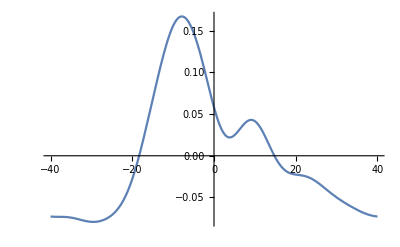

```mathematica
Plot[f[x],{x,-40,40}]
```